# Introduction to 2D graphics

Math 213 - Math with Mathematica
Christopher Hanusa

## Overview

In this tutorial, we start working with 2D graphics objects as building blocks with an eye toward creating animations using Manipulate.

## Graphics objects

### Syntax

When you are constructing graphics, you build them piece by piece by creating a list of Graphics primitives.  There are many primitives, and we’ll talk about many of them below.  When you want to display these pieces together, wrap the list in a Graphics command.  This will generate a visual representation of your primitives in layers from bottom to top.

### Modifying primitives

There are many many properties, settings, and options available for Graphics Objects. We’ll discuss some of them below. 
You may ask: “Can I make my object look like _______ ?” 
My answer: “Probably!”
The Documentation Center is your friend!!!!

### Geometry

To make your graphics, it will take quite a bit of thinking and strategizing.  The most important thing to understand is that we will be placing 2D (and later 3D) objects using Cartesian coordinates.  [Think: (x,y) in 2D or (x,y,z) in 3D.]  You will need to plan out the positions of all the points.  This may involve trigonometry, for instance, to find the placement of a point on a circle.

### Show

If you have multiple graphics that you’d like to combine together, use the Show command to display them all at the same time.  The most important aspect of the Show command is that the combined object inherits the settings of the first graphic.

## 0D objects: Points

A point is a zero-dimensional object; generate one using the Point command.
Remember that all graphics primitives need to be included in a Graphics command to be displayed.

```mathematica
Point[{0,0}]
```

Point[{0,0}]

```mathematica
Graphics[Point[{0,0}]]
```

-Graphics-

Graphics only takes as an input ONE object, so when you have more than one primitive to display, put them in a list.

```mathematica
Graphics[    {Point[{0,0}],Point[{1,1}]}    ]
```

-Graphics-

The Map command may come in handy.
Here we use Map to apply Point to many coordinate pairs.

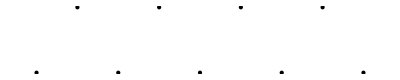

```mathematica
pointlist={{0,0},{1,1},{2,0},{3,1},{4,0},{5,1},{6,0},{7,1},{8,0}};
Graphics[Map[Point,pointlist]]
```

Do Now: Navigate to the Documentation Center entry for Point, and look at the “Neat Examples” at the bottom.

## Color

Certain colors are predefined in Mathematica like Red, Orange, Yellow, etc.  
Furthermore, you can create any color using, among others, Hue and RGBColor.  
And you make colors lighter and darker using Lighter and Darker.
You can see the colors that are available in guide/Colors.

You change color by putting the color’s name before the primitive.

```mathematica
Graphics[{Red,Point[{0,0}]}]
```

-Graphics-

I suggest using braces to delimit where the color applies.  
Here I have included the option PointSize, which specifies the size of the point.

```mathematica
Graphics[{PointSize[.2],
{Lighter[Red],Point[{0,0}]},
{Orange,Point[{1,0}]},
{Darker[Yellow], Point[{2,0}]}
}]
```

-Graphics-

A nice use of the command Hue is to make a rainbow of colors.  Hue takes as input any number from zero to one.
Here you can see that we place a point at {i,0} with color Hue[i/7].

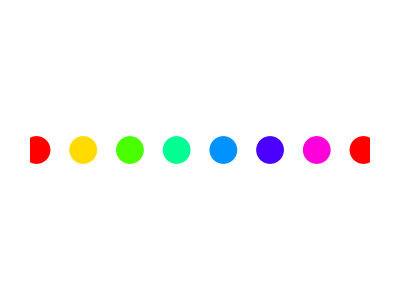

```mathematica
Graphics[{PointSize[.05],
Table[{Hue[i/7],Point[{i,0}]},{i,0,7}]
}]
```

We can also change how transparent the shape is using the Opacity command.

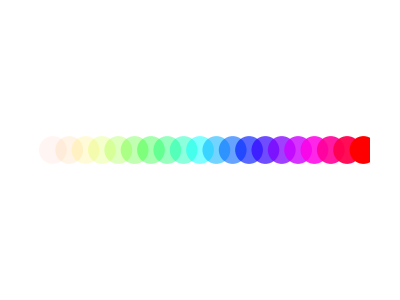

```mathematica
Graphics[{PointSize[.05],
Table[{Hue[i/20],Opacity[i/20],Point[{i,0}]},{i,0,20}]
}]
```

```mathematica
?Hue
```

Hue[h] is a graphics directive which specifies that objects which follow are to be displayed, in a color corresponding to hue h. 
Hue[h,s,b] specifies colors in terms of hue, saturation, and brightness. 
Hue[h,s,b,a] specifies opacity a.

## 1D objects: Line segments

To create line segments, use the Line command.  The input is a list of coordinates of initial, intermediate, and terminal vertices of the sequence of line segments you wish to display.
Remember that all graphics objects need to be included in a Graphics command to be displayed.

```mathematica
Line[{{0,0},{1,1}}]
```

Line[{{0,0},{1,1}}]

```mathematica
Graphics[Line[{{0,0},{1,1}}]]
```

-Graphics-

A sequence of line segments creates a path.  If you connect the points {{0,0},{1,1},{2,0},{3,1},{4,0},{5,1},{6,0},{7,1},{8,0}},

```mathematica
Graphics[Map[Point,{{0,0},{1,1},{2,0},{3,1},{4,0},{5,1},{6,0},{7,1},{8,0}}]]
```

-Graphics-

It gives a zigzag pattern:

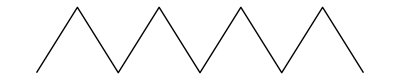

```mathematica
Graphics[Line[{{0,0},{1,1},{2,0},{3,1},{4,0},{5,1},{6,0},{7,1},{8,0}}]]
```

By default, the line segments are displayed without axes or identifying markers.  So if you display the line segment from (0,0) to (1,1) it looks the same as the segment from (1,0) to (2,1).

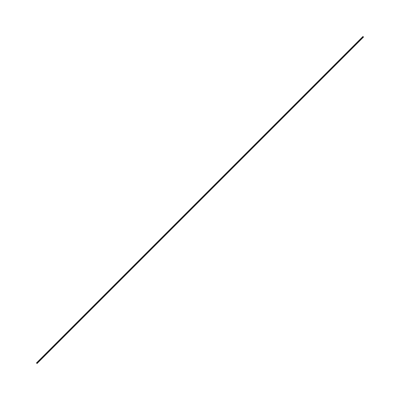
{-Graphics-,-Graphics-}

```mathematica
{Graphics[Line[{{0,0},{1,1}}]],Graphics[Line[{{1,0},{2,1}}]]}
```

To rectify that, use the PlotRange and Axes options.
Here is some code that will display a line segment in the window [-2,2]x[-2,2], displaying axes:

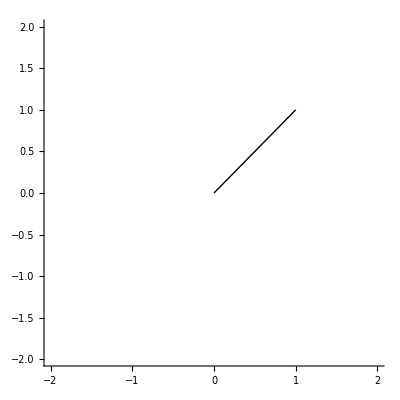
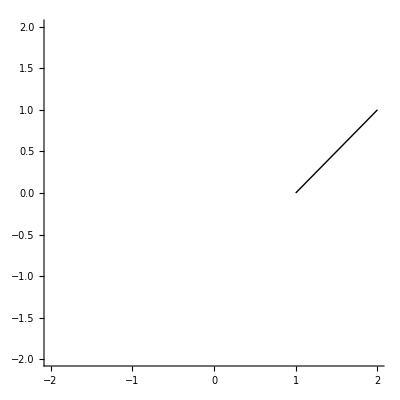

```mathematica
{Graphics[Line[{{0,0},{1,1}}],PlotRange->{{-2,2},{-2,2}},Axes->True],
Graphics[Line[{{1,0},{2,1}}],PlotRange->{{-2,2},{-2,2}},Axes->True]}
```

Another important option is ImageSize, in case you want to specify the size of your graphic.

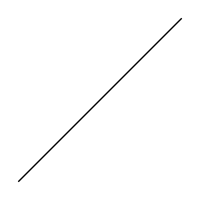
{-Graphics-,-Graphics-}

```mathematica
{Graphics[Line[{{0,0},{1,1}}],ImageSize->100],
Graphics[Line[{{0,0},{1,1}}],ImageSize->200]}
```

Do Now: Navigate to the Documentation Center entry for Line, and look at the “Neat Examples” at the bottom.

## Comprehension Questions

### 1. Instead of typing each coordinate (as above), use a Table command to create this ZigZag pattern: -Graphics-

#### Hint 1 (Expand cell to see)

Use the first coordinate as the indexing variable in your Table command.

#### Hint 2 (Expand cell to see)

Use an If statement and a Q command to condition on whether the first entry is even or odd.

### 2. Modify your code from Question 1 to make the zigzag pattern longer (from (0,0) to (100,0)), using a thick purple line!

### 3. Use Table commands to draw a grid of vertical and horizontal lines that looks like graph paper, just like this.

-Graphics-

#### Hint 1 (Expand cell to see)

Combine one Table command for the horizontal line segments and one Table command for the vertical line segments.

#### Hint 2 (Expand cell to see)

How do you create TWO parallel horizontal lines?  What changed from line one to line two?  Use this to figure out what your indexing variable should be in the Table command.

## Challenge Question

Work on this question if you were able to complete the first three questions quickly.  Otherwise skip it.

### 4. Create a Manipulate command that displays the line segment that has as its endpoints the origin (0,0) and a user-specified position (x,y). You should use a PlotRange option so that the origin does not move. I suggest creating the same graphic three times, each using a different control: (Learn more about the controls in the Manipulate documentation.) (a) Use a 1D slider for each of x and y. (b) Use a 2D slider for the (x,y) pair. (c) Use a locator to interactively move the point (x,y).

## Some answers to Comprehension Questions. Don’t Peek until you tried them!

### Question 3

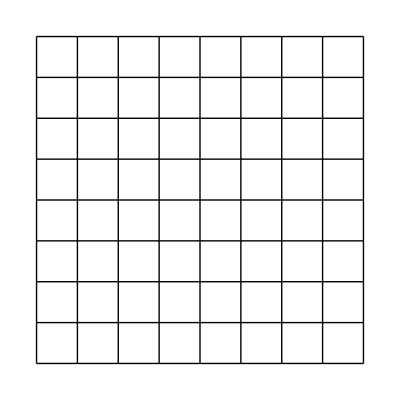

```mathematica
Graphics[{
Table[Line[{{0,i},{8,i}}],{i,0,8}],
Table[Line[{{i,0},{i,8}}],{i,0,8}]
}]
```

### Question 4(a)

```mathematica
Manipulate[Graphics[Line[{{0,0},{x,y}}],PlotRange->{{-2,2},{-2,2}},Axes->True],{x,-2,2},{y,-2,2}]
```

## Circles

To display a point in space, you can use the Point command, but instead you probably use the Disk command, or its friend the Circle command, which you can see give filled in or empty circles (or ellipses, or parts thereof).

```mathematica
?Disk
```

Disk[{x,y},r] represents a disk of radius r centered at {x,y}.
Disk[{x,y}] gives a disk of radius 1. 
Disk[{x,y},{r_x,r_y}] gives an axis-aligned elliptical disk with semiaxes lengths r_x and r_y.
Disk[{x,y},…,{θ_1,θ_2}] gives a sector of a disk from angle θ_1 to θ_2.

```mathematica
?Circle
```

Circle[{x,y},r] represents a circle of radius r centered at {x,y}.
Circle[{x,y}] gives a circle of radius 1. 
Circle[{x,y},{r_x,r_y}] gives an axis-aligned ellipse with semiaxes lengths r_x and r_y.
Circle[{x,y},…,{θ_1,θ_2}] gives a circular or ellipse arc from angle θ_1 to θ_2.

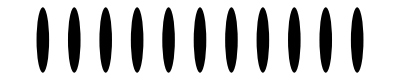

```mathematica
Graphics[Table[Disk[{i,0},.2],{i,0,10}]]
```

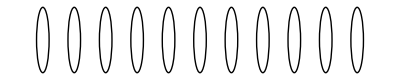

```mathematica
Graphics[Table[Circle[{i,0},.2],{i,0,10}]]
```

When you apply a color to a disk primitive, then it colors the whole object; if you want the boundary to be a different color, use the EdgeForm option:

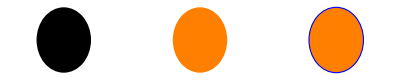

```mathematica
Graphics[{
{Disk[{0,0},.2]},
{Orange,Disk[{1,0},.2]},
{Orange,EdgeForm[{Blue,Thick,Dashed}],Disk[{2,0},.2]}
}]
```

Do Now: Navigate to the Documentation Center entry for Disk, and look at the “Neat Examples” at the bottom.

## Comprehension Questions

### 5. Create a Manipulate command that draws the unit circle and a point that travels along the boundary of the circle.

#### Hint (Expand cell to see)

A point on the unit circle has coordinates (cos(θ),sin(θ)) as θ varies from 0 to 2Pi.

### 6. Modify your answer to Question 6 so that the circle is filled in with a color other than white and has a different color on the border.

#### Hint (Expand cell to see)

A point on the unit circle has coordinates (cos(θ),sin(θ)) as θ varies from 0 to 2Pi.

## Challenge Questions

Work on these questions if you were able to complete questions 5 and 6 quickly.  Otherwise skip them.

### 7. Modify your answer from Question 4 so that there are endpoints visible on the line segment.

### 8. (Much more difficult) Add to your answer from Question 7 a dynamic line segment tangent to this unit circle through the specified point.

#### Hint 1 (Expand cell to see)

You will need to do some calculations!  What is the slope of the tangent line to a circle?

#### Hint 2 (Expand cell to see AFTER you think deeply about the question in Hint 1)

The slope of the tangent line is -x/y because it is the negative reciprocal of the line through the origin and the point, which has slope y/x.
Now you need to create a line segment through the point (x,y) with slope -x/y.  How do you do that?

#### Hint 3 (Expand cell to see AFTER you think deeply about the question in Hint 2)

To go from a fixed point (x,y) along a line of slope -x/y corresponds to walking from (x,y) in the direction (y,-x) (or toward (-y,x)) for some distance.  So ONE of the endpoints of your line segment might be (x,y)+(y,-x).

## Some Answers. Don’t Peek until you tried them!

### Question 5

```mathematica
Manipulate[Graphics[{Circle[{0,0},1],Disk[{Cos[theta],Sin[theta]},.05]},PlotRange->1.5],{theta,0,2Pi}]
```

### Question 8

```mathematica
Manipulate[Graphics[{
{EdgeForm[{Black,Thick}],Lighter[Blue],Disk[{0,0},1]},
Disk[{Cos[theta],Sin[theta]},.03],
Arrowheads[{-.05,.05}],Thick,
Arrow[{
{Cos[theta],Sin[theta]}-{Sin[theta],-Cos[theta]},
{Cos[theta],Sin[theta]}+{Sin[theta],-Cos[theta]}
}]
},PlotRange->1.5],{theta,0,2Pi}]
```

## Polygons

A Line primitive can be used to give a closed unfilled polygon if the first and last coordinates are the same.
If you want to have a closed filled polygon, use the Polygon primitive.  (So Polygon is to Line as Disk is to Circle.)
You can see that while the Line must have the first and last coordinates the same, this is not necessary in Polygon.
And use EdgeForm just as in Disk.

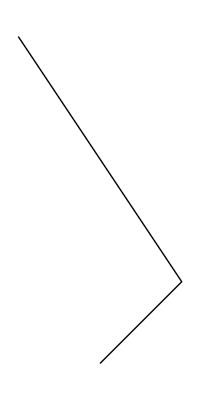
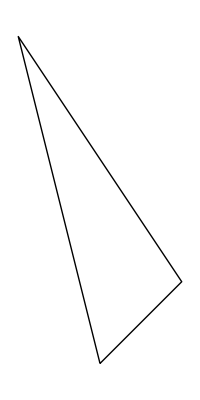
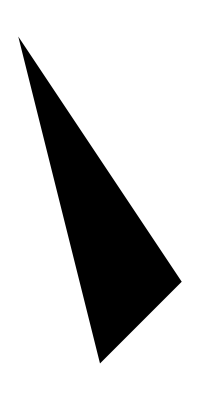
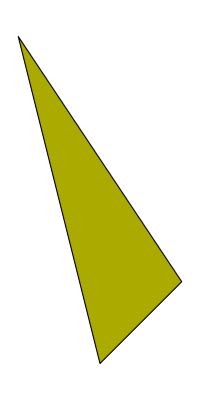

```mathematica
{
Graphics[Line[{{0,1},{1,2},{-1,5}}]],
Graphics[Line[{{0,1},{1,2},{-1,5},{0,1}}]],
Graphics[Polygon[{{0,1},{1,2},{-1,5}}]],
Graphics[{EdgeForm[{Black,Thin}],Darker[Yellow],Polygon[{{0,1},{1,2},{-1,5}}]}]
}
```

A regular n-gon is a polygon where each of the n edges are the same length and each of the n angles are the same.  Instead of guessing the coordinates for the vertices of a regular polygon, instead use Mathematica’s computing ability to calculate n equally spaced points on a circle.  Since there are n vertices to place on a circle with 2π radians, then place the vertices at coordinates (cos((2π i)/n),sin((2π i)/n)) as i ranges from 0 to n.  When n=5, we have the coordinates:

```mathematica
radius=1
Module[{n=5},Table[{radius*Cos[2Pi i/n],radius*Sin[2 Pi i/n]},{i,0,n}]]
```

1

{{1,0},{1/4 (-1+√5),√(5/8+(√5)/8)},{1/4 (-1-√5),√(5/8-(√5)/8)},{1/4 (-1-√5),-√(5/8-(√5)/8)},{1/4 (-1+√5),-√(5/8+(√5)/8)},{1,0}}

Here we let n vary in a colorful Manipulate command.  (Note the use of EdgeForm and Thickness.)

```mathematica
Manipulate[radius=1; (* `radius' specifies the radius of the circle on which the vertices are placed*)
Graphics[{EdgeForm[{Black,Thickness[.04]}],Hue[(n-3)/9],  
(* Hue gives a color of the rainbow; the (n-3)/9 was chosen to make the colors pretty. *)
Polygon[Table[{radius*Cos[2Pi i/n],radius*Sin[2 Pi i/n]},{i,0,n}]]
}],{n,3,10,1}]
```

Do Now: Navigate to the Documentation Center entry for Polygon, and look at the “Neat Examples” at the bottom.

## Comprehension Questions

### 9. When we created regular n-gons, we drew the n points on the circle and connected each vertex with its two neighbors. What will happen if you instead connect each vertex not with its neighbors but with the neighbors of its neighbors (distance two away)? Try it!

## Curves

### Plot

When you want to plot the graph of a function, use the Plot command.  Use the PlotRange option to specify the range of possible values on the y-axis and the PlotStyle option to change the style of the curve.

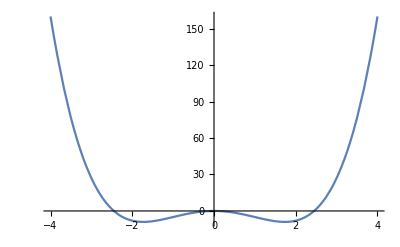
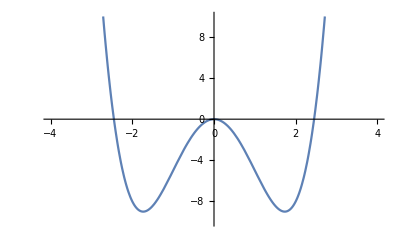
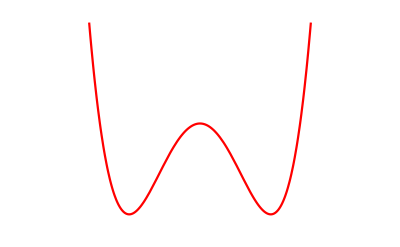

```mathematica
{
Plot[x^4-6x^2,{x,-4,4}],
Plot[x^4-6x^2,{x,-4,4},PlotRange->{-10,10}],
Plot[x^4-6x^2,{x,-4,4},PlotRange->{-10,10},PlotStyle->Red,Axes->False]
}
```

Do Now: Navigate to the Documentation Center entry for Plot, and explore all the options that are possible.

### ParametricPlot

Alternatively your curve might not be a function, but instead be defined as a parametric curve, in which case you can use ParametricPlot.
(Here we have searched Mathematica for “Homer Simpson curve”; expand the cell to see the code.

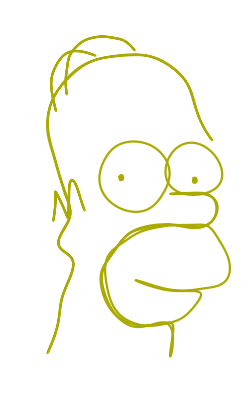

```mathematica
ParametricPlot[{{131.375-1.375 Sin[1.54545-8. t]-0.75 Sin[1.57143-6. t]-0.9 Sin[1.54545-5. t]+38.7778 Sin[1.57143+t]+1.41667 Sin[1.6+2. t]+7.02439 Sin[1.6+3. t]+6.9 Sin[1.6+4. t]+1.6 Sin[1.625+7. t]+0.571429 Sin[1.64706+9. t]+0.571429 Sin[1.72727+10. t],487.727-0.363636 Sin[1.4-10. t]-0.6875 Sin[1.07692-7. t]-43.7273 Sin[1.54545-4. t]-11.1429 Sin[1.52941-3. t]+19.9091 Sin[1.57143+t]+2.14286 Sin[1.63636+2. t]+6.27273 Sin[1.57143+5. t]+2.58333 Sin[4.7+6. t]+0.625 Sin[1.58333+8. t]+1.11111 Sin[1.54545+9. t]},{124.5-0.75 Sin[1.57143-5. t]-54. Sin[1.57143-1. t]+29.625 Sin[1.57143+2. t]+4.72727 Sin[4.71429+3. t]+4.22222 Sin[1.57143+4. t],872.952-5.76923 Sin[1.55556-4. t]-26.4 Sin[1.57143-2. t]-83. Sin[1.57143-1. t]+0.142857 Sin[4.7+3. t]+0.125 Sin[1.27273+5. t]},{201.571-1.77778 Sin[1.55556-5. t]-2.5 Sin[1.55556-3. t]+97.625 Sin[4.71429+t]+26.4545 Sin[1.57143+2. t]+3.28571 Sin[1.57143+4. t]+0.947368 Sin[1.57143+6. t]+0.4 Sin[4.69231+7. t]+1.04348 Sin[1.55556+8. t]+0.037037 Sin[0.454545+9. t]+0.363636 Sin[1.57143+10. t]+0.0133333 Sin[0.625+11. t],929.375+63.6667 Sin[4.71429+t]+40.4444 Sin[4.71429+2. t]+1.95455 Sin[4.66667+3. t]+7.52381 Sin[4.71429+4. t]+0.25 Sin[4.35294+5. t]+4.03333 Sin[4.7+6. t]+0.111111 Sin[2.83333+7. t]+2.27273 Sin[4.69231+8. t]+0.166667 Sin[4.44444+9. t]+1.16667 Sin[4.7+10. t]+0.0714286 Sin[1.96429+11. t]},{222.111-0.636364 Sin[1.3-13. t]+187.688 Sin[4.71429+t]+122.4 Sin[1.57143+2. t]+49.2727 Sin[4.7+3. t]+19.5714 Sin[4.63636+4. t]+7.57143 Sin[1.54545+5. t]+1.91667 Sin[4.55556+6. t]+8.54545 Sin[4.63636+7. t]+7.36364 Sin[4.55556+8. t]+4.41667 Sin[4.6+9. t]+3.47619 Sin[1.44444+10. t]+2.14286 Sin[1.2+11. t]+5.28571 Sin[1.4+12. t]+0.555556 Sin[3.85714+14. t]+5.14286 Sin[4.5+15. t]+2.95652 Sin[4.36364+16. t]+1.55556 Sin[4.57143+17. t],597.143-0.571429 Sin[1.55556-13. t]+354.875 Sin[4.7+t]+148.833 Sin[4.69231+2. t]+47.8182 Sin[1.6+3. t]+53.4667 Sin[4.7+4. t]+5.02778 Sin[4.33333+5. t]+24.0115 Sin[4.66667+6. t]+3.625 Sin[4.3125+7. t]+10.4167 Sin[4.7+8. t]+0.8 Sin[4.41667+9. t]+1.97872 Sin[4.69231+10. t]+0.3 Sin[1.28571+11. t]+2.6 Sin[4.66667+12. t]+1.95238 Sin[4.4+14. t]+0.8 Sin[4.4+15. t]+2.8 Sin[4.54545+16. t]+2.42857 Sin[4.44444+17. t]},{397.167+89.0526 Sin[1.52632+t]+104.4 Sin[1.45455+2. t]+63.9167 Sin[4.53846+3. t]+23.2727 Sin[4.42857+4. t]+20.2 Sin[4.36364+5. t]+20.375 Sin[4.3+6. t]+6.72727 Sin[4.08333+7. t]+8.75 Sin[4.1+8. t]+1.46667 Sin[2.07143+9. t]+4.3 Sin[4.+10. t]+2.28571 Sin[1.2+11. t]+0.52381 Sin[3.92857+12. t]+0.75 Sin[3.7+13. t]+1.3 Sin[3.85714+14. t],305.024-1.75 Sin[0.727273-14. t]-2.84615 Sin[1.5-12. t]+213.182 Sin[1.52381+t]+27.4783 Sin[4.66667+2. t]+4.83333 Sin[1.47619+3. t]+22.2727 Sin[1.25+4. t]+12.0625 Sin[1.4+5. t]+9.5 Sin[4.57143+6. t]+3.8 Sin[1.88889+7. t]+14.5217 Sin[4.375+8. t]+3.66667 Sin[1.90909+9. t]+7.06667 Sin[4.4+10. t]+3.46667 Sin[1.58333+11. t]+3.5 Sin[1.23077+13. t]},{295.25-0.111111 Sin[1.4-10. t]-0.222222 Sin[1.22222-6. t]+1.81818 Sin[1.06667+t]+0.538462 Sin[3.75+2. t]+4.30769 Sin[2.77778+3. t]+0.166667 Sin[3.73333+4. t]+0.3125 Sin[2.375+5. t]+0.4 Sin[0.3125+7. t]+0.416667 Sin[3.4+8. t]+0.25 Sin[3.+9. t],557.417-0.428571 Sin[0.1-9. t]-0.125 Sin[0.357143-5. t]-1.125 Sin[1.52941-2. t]+2.57143 Sin[1.27273+t]+4.98 Sin[4.625+3. t]+0.230769 Sin[2.11111+4. t]+0.4 Sin[4.0625+6. t]+0.529412 Sin[0.25+7. t]+0.3125 Sin[3.38462+8. t]+0.222222 Sin[2.9+10. t]},{517.125-0.166667 Sin[0.727273-5. t]+0.625 Sin[1.2+t]+2.6 Sin[3.21429+2. t]+3.33333 Sin[3.5+3. t]+1.3 Sin[0.96+4. t]+0.166667 Sin[1.8+6. t]+0.25 Sin[2.84615+7. t]+0.125 Sin[3.25+8. t]+0.111111 Sin[0.777778+9. t]+0.222222 Sin[2.52+10. t]+0.1 Sin[0.111111+11. t],549.286-0.037037 Sin[1.-11. t]-0.166667 Sin[0.363636-10. t]-0.2 Sin[0.181818-9. t]-0.35 Sin[0.5-5. t]-3.64286 Sin[1.03571-3. t]+3.28571 Sin[3.6+t]+2.77778 Sin[4.41667+2. t]+1.5 Sin[2.73333+4. t]+0.2 Sin[3.27273+6. t]+0.0833333 Sin[4.66667+7. t]+0.3 Sin[2.11111+8. t]},{432.25-1.30769 Sin[1.2-12. t]-2.14286 Sin[0.961538-11. t]-1.85714 Sin[0.214286-10. t]-3.57143 Sin[0.692308-6. t]-109.667 Sin[0.470588-1. t]+108.875 Sin[2.+2. t]+36.6429 Sin[1.25+3. t]+12.2222 Sin[0.375+4. t]+5.375 Sin[0.2+5. t]+3.30769 Sin[3.81818+7. t]+3.0625 Sin[0.846154+8. t]+2.2 Sin[0.285714+9. t]+0.714286 Sin[3.23077+13. t],261.8-1.14286 Sin[0.333333-13. t]-0.692308 Sin[0.8-11. t]-1.68421 Sin[1.41667-9. t]-1.83333 Sin[0.692308-8. t]-11.2667 Sin[0.470588-3. t]+114.625 Sin[4.58333+t]+66.9 Sin[0.307692+2. t]+11.0909 Sin[2.04167+4. t]+3.44444 Sin[0.125+5. t]+2.77778 Sin[0.857143+6. t]+4.3 Sin[0.047619+7. t]+0.947368 Sin[0.692308+10. t]+0.222222 Sin[2.06667+12. t]},{514.182+85.4 Sin[2.02222+t]+0.272727 Sin[3.5+2. t],577.357-7.02632 Sin[0.3-2. t]+78.125 Sin[3.64706+t]},{336.364-1.11111 Sin[0.7-4. t]-0.538462 Sin[0.833333-3. t]-104.571 Sin[0.571429-1. t]+2.03226 Sin[0.0212766+2. t]+1.6875 Sin[2.75+5. t],562.75+105.385 Sin[4.16667+t]+1.95238 Sin[4.01961+2. t]+0.6875 Sin[0.615385+3. t]+0.692308 Sin[2.88889+4. t]+1.2 Sin[0.785714+5. t]}},{t,0,2 π},Axes->False,PlotStyle->Darker[Yellow]]
```

Plot and ParametricPlot require that you already know the function.  Often you instead have points that you would like to serve as a guide for a smooth curve and you need Mathematica to create it.  There are two good options available, Interpolation and BSplineCurve.

### Interpolation

Interpolation will fit a function perfectly through the desired points.  (The output is a piecewise-defined function.)
The higher you set the InterpolationOrder, the smoother the curve.

```mathematica
?Interpolation
```

Interpolation[{f_1,f_2,…}] constructs an interpolation of the function values f_i, assumed to correspond to x values 1, 2, … . 
Interpolation[{{x_1,f_1},{x_2,f_2},…}] constructs an interpolation of the function values f_i corresponding to x values x_i.
Interpolation[{{{x_1,y_1,…},f_1},{{x_2,y_2,…},f_2},…}] constructs an interpolation of multidimensional data.
Interpolation[{{{x_1,…},f_1,df_1,…},…}] constructs an interpolation that reproduces derivatives as well as function values.
Interpolation[data,x] find an interpolation of data at the point x.

```mathematica
pts={{0,0},{1,1},{2,-1},{3,0},{4,-2},{5,1}};
```

```mathematica
interp=Interpolation[pts,InterpolationOrder->5]
```

InterpolatingFunction[{{0, 5}}, <>]

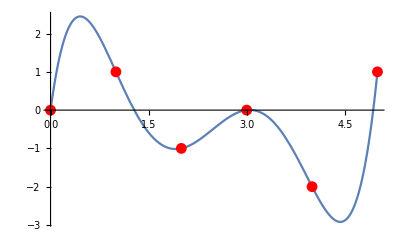

```mathematica
Show[
Plot[interp[x],{x,0.,5.}],
ListPlot[pts,PlotStyle->Red]]
```

### BSplineCurve

BSplineCurve uses the points as a guide to specify a very smooth curve.  (The output is a graphics primitive and the output does not have to be a function.)

```mathematica
?BSplineCurve
```

BSplineCurve[{pt_1,pt_2,…}] is a graphics primitive that represents a nonuniform rational B-spline curve with control points pt_i.

```mathematica
pts={{0,0},{1,1},{2,-1},{3,0},{4,-2},{5,1}};
```

```mathematica
Graphics[{BSplineCurve[pts],Green,Line[pts],Red,Point[pts]}]
```

-Graphics-

You can use the SplineClosed option to close up the curve in a smooth fashion.

```mathematica
Graphics[{BSplineCurve[pts,SplineClosed->True],Green,Line[Append[pts,pts[[1]]]],Red,Point[pts]}]
```

-Graphics-

Do Now: Navigate to the Documentation Center entry for BSplineCurve, and look at the “Neat Examples” at the bottom.

## Comprehension Questions

### 10. Similar to Question 6, create a Manipulate command that draws the curve y=x^3+2x^2+x+1 and moves a point that travels along the curve.

Important reminder: When you need to combine multiple Graphics objects, use the Show command.

## RegionPlot

One final way to plot a closed region in 2D space is to use RegionPlot.  It gives all the points in the specified region that satisfy your given requirements

```mathematica
?RegionPlot
```

RegionPlot[pred,{x,x_min,x_max},{y,y_min,y_max}] makes a plot showing the region in which pred is True.

Here is another way to make a circle.

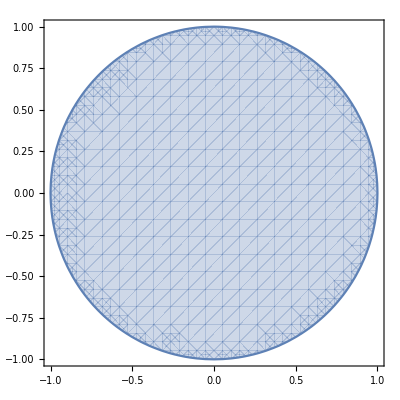

```mathematica
RegionPlot[x^2+y^2≤1,{x,-1,1},{y,-1,1}]
```

To specify multiple constraints, use the && operator.

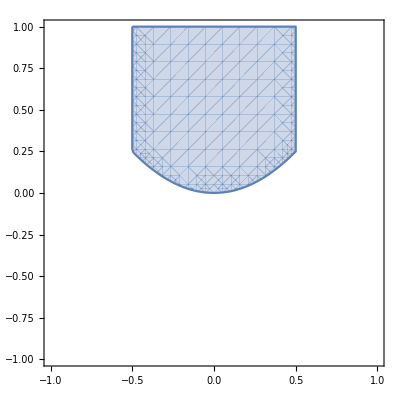

```mathematica
RegionPlot[y≥x^2&&-.5≤x≤.5,{x,-1,1},{y,-1,1}]
```

Do Now: Navigate to the Documentation Center entry for RegionPlot, and look at the “Neat Examples” at the bottom.

## Comprehension Questions

### 11. Use RegionPlot to draw the region that is between the two curves y=Sqrt[x] and y=x^2 for x between 0 and 1.

## Work to understand this example.

### Example. Create a Sierpinski Carpet.

```mathematica
Apply[And,Flatten[Table[(Max[Abs[x-i],Abs[y-j]]≥1/9),{i,-2/3,2/3,2/3},{i,-2/3,2/3,2/3}],1]]
```

Max[Abs[2/3+x],Abs[-j+y]]≥1/9&&Max[Abs[x],Abs[-j+y]]≥1/9&&Max[Abs[-2/3+x],Abs[-j+y]]≥1/9&&Max[Abs[2/3+x],Abs[-j+y]]≥1/9&&Max[Abs[x],Abs[-j+y]]≥1/9&&Max[Abs[-2/3+x],Abs[-j+y]]≥1/9&&Max[Abs[2/3+x],Abs[-j+y]]≥1/9&&Max[Abs[x],Abs[-j+y]]≥1/9&&Max[Abs[-2/3+x],Abs[-j+y]]≥1/9

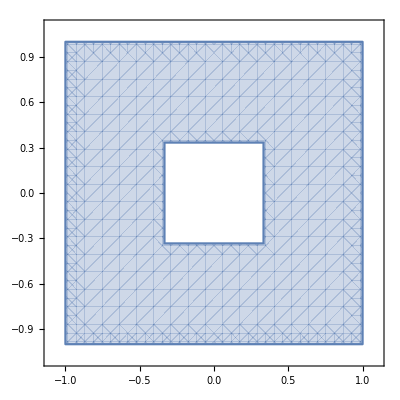

```mathematica
RegionPlot[(Max[Abs[x],Abs[y]]≤1)&&(Max[Abs[x],Abs[y]]≥1/3),{x,-1.1,1.1},{y,-1.1,1.1}]
```

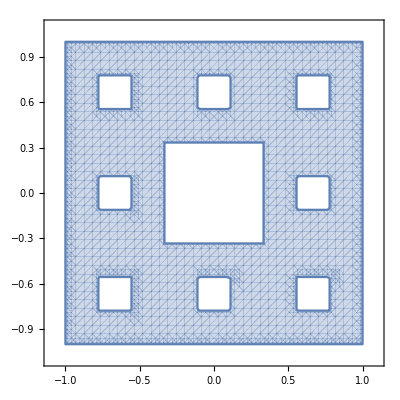

```mathematica
RegionPlot[(Max[Abs[x],Abs[y]]≤1)&&(Max[Abs[x],Abs[y]]≥1/3)&&Apply[And,Flatten[Table[(Max[Abs[x-i],Abs[y-j]]≥1/9),{i,-2/3,2/3,2/3},{j,-2/3,2/3,2/3}],1]],{x,-1.1,1.1},{y,-1.1,1.1},PlotPoints->40]
```

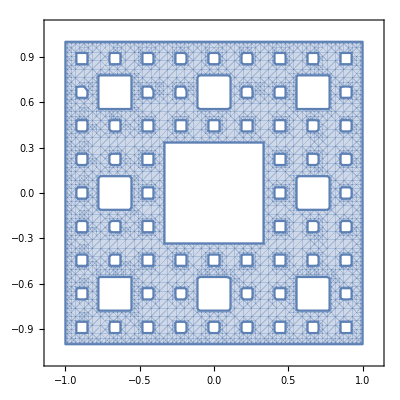

```mathematica
RegionPlot[(Max[Abs[x],Abs[y]]≤1)&&(Max[Abs[x],Abs[y]]≥1/3)&&Apply[And,Flatten[Table[(Max[Abs[x-i],Abs[y-j]]≥1/9),{i,-2/3,2/3,2/3},{j,-2/3,2/3,2/3}],1]]&&
Apply[And,Flatten[Table[(Max[Abs[x-i],Abs[y-j]]≥1/27),{i,-8/9,8/9,2/9},{j,-8/9,8/9,2/9}],1]]
,{x,-1.1,1.1},{y,-1.1,1.1},PlotPoints->40]
```